# Seminarska naloga iz računalniških orodij v matematiki Denis Benčič

## V seminarski nalogi bom rešil štiri matematične naloge v stilu kolokvija z uporabo Mathematice iz snovi teorije množic, teorije števil, matematične analize in linearne algebre z namenom predstavitve, kaj vse Mathematica zmore in česar ne zmore. V prvi nalogi bom predstavil elementarne operacije nad množicami. V drugi nalogi bom dokazal tri manj očitna dejstva, ki veljajo za naravna števila s pomočjo faktorizacije, polinomskega deljenja in matematične indukcije. V tretji nalogi bom analiziral bolj kompliciran primer realne funkcije realne spremenljivke s pomočjo teorije funkcij in infinitezimalnega računa in jo narisal v ravnini. V četrti nalogi bom s pomočjo analitične geometrije in vektorjev izračunal obseg, ploščino, notranje kote in središče očrtane krožnice danega trikotnika v prostoru, pri čemer si bom pomagal s programiranjem novih funkcij. Trikotnik in njemu očrtano krožnico bom nato izrisal v ravnini, saj se izkaže, da Mathematica nima vgrajene funkcije za izris krožnice v prostoru (1).

1. (2) Naj bo U={1,2,...,12} univerzalna množica. Podane so množice A={1,2,4,7,9,11}, B={2,4,5,8,9,12} in C={3,7,9,10}. Določi naslednje množice:

a) A∪B

Definirajmo množici A in B ter določimo njuno unijo:

```mathematica
A={1,2,4,7,9,11};
B={2,4,5,8,9,12};
Union[A,B]
```

{1,2,4,5,7,8,9,11,12}

b) A∩B

Podobno kot prej določimo presek množic:

```mathematica
Intersection[A,B]
```

{2,4,9}

c) A\B

Podobno kot prej določimo razliko množic:

```mathematica
Complement[A,B]
```

{1,7,11}

d) A^c

Določimo komplement množice A. To lahko določimo kot razliko med univerzalno množico, ki jo moramo najprej definirati, in množico A:

```mathematica
U=Range[12];
```

```mathematica
Complement[U,A]
```

{3,5,6,8,10,12}

e) A∩B^C

Podobno kot v prejšnjih primerih določimo zgornjo množico:

```mathematica
Intersection[A,Complement[U,B]]
```

{1,7,11}

f) (A∩B^C)∪C^C

Podobno kot v prejšnjih primerih določimo zgornjo množico, še prej pa definirajmo množico C (pri tem uporabimo malo črko, saj velika je zasedena):

```mathematica
c={3,7,9,10};
Union[Intersection[A,Complement[U,B]], Complement[U,c]]
```

{1,2,4,5,6,7,8,11,12}

2. Naj bodo a, b, c in d štiri zaporedna naravna števila.

a) Dokaži, da vsota treh zaporednih števil ni praštevilo.

Po definiciji je praštevilo naravno število, različno od 1, ki je deljivo zgolj s samim sabo in z 1. Naj bo n neko fiksno naravno število. Definirajmo zaporedna naravna števila a, b, c in d s pomočjo števila n:

```mathematica
a=n;
b=n+1;
c=n+2;
d=n+3;
```

Poskusimo sešteti števila a, b, c in d in vsoto faktorizirati:

```mathematica
Factor[a+b+c+d]
```

2 (3+2 n)

Iz faktorizacije je razvidno, da je zgornja vsota deljiva z 2. Od tod lahko po definiciji praštevila zaključimo, da vsota štirih naravnih števil ni praštevilo, lahko pa uporabimo tudi ustrezno funkcijo:

```mathematica
PrimeQ[Factor[a+b+c+d]]
```

False

Torej vsota treh zaporednih števil res ni praštevilo.

b) Dokaži, da d^2 deli a+b^2+c^3.

Za začetek poskusimo razčleniti števili d^2 in a+b^2+c^3 in ju shraniti v novi spremenljivki:

```mathematica
A=Expand[d^2]
B=Expand[a+b^2+c^3]
```

9+6 n+n^2

9+15 n+7 n^2+n^3

Kot vidimo, imamo števili predstavljeni kot polinoma naravne spremenljivke n. Dovolj bo pokazati, da sta polinoma deljiva tako, da izvedemo polinomsko deljenje z ostankom:

```mathematica
PolynomialMod[B, A]
```

0

Ostanek deljenja obeh polinomov je 0, iz česar sledi, da sta števili d^2 in a+b^2+c^3 deljivi. Torej d^2 res deli a+b^2+c^3.

c) S popolno indukcijo dokaži, da je produkt štirih zaporednih naravnih števil sodo število.

Definirajmo produkt in z bazo indukcije dokažimo, da zgornja trditev velja za n = 1:

```mathematica
P:=a*b*c*d 
P /. n->1
```

24

Dobljen produkt je očitno sod, lahko se pa prepričamo tudi z ustrezno funkcijo:

```mathematica
EvenQ[P /.n->1]
```

True

Naredimo indukcijski korak, definiramo nov produkt in vse spremenljivke n nadomestimo z n + 1:

```mathematica
Q:=P /.n->n+1
```

Oba produkta v razčlenjeni obliki poskusimo medseboj sešteti in vsoto faktorizirati:

```mathematica
Factor[Expand[P]+Expand[Q]]
```

2 (1+n) (2+n)^2 (3+n)

Kot vidimo iz faktorizacije, je vsota produktov soda. Za prvi produkt smo predpostavili, da je sod in dobili sodo vsoto. Iz sode vsote sledi, da je drugi produkt ravno tako sod, saj je vsota dveh števil soda natanko tedaj, ko sta obe števili sodi. Torej je produkt štirih zaporednih naravnih števil res sod.

3. Dana je funkcija f(x) = arctan((ⅇ^x-ⅇ^-x)/(ⅇ^x+ⅇ^-x))

a) Določi ničle funkcije f.

Definirajmo funkcijo f in izračunajmo njene ničle:

```mathematica
f[x_] := ArcTan[(E^(x)-E^(-x))/(E^x+E^(-x))]
```

```mathematica
f[x]
```

ArcTan[(-ⅇ^-x+ⅇ^x)/(ⅇ^-x+ⅇ^x)]

```mathematica
Solve[f[x]==0, x, Reals]
```

{{x→0}}

b) Določi definicijsko območje funkcije f.

Kot vidimo je funkcija f kompozitum krožne in racionalne funkcije z eksponentnimi spremenljivkami. Ker so racionalne funkcije definirane na celi množici ℝ razen v polih, poskusimo določiti pole:

```mathematica
Solve[Denominator[Tan[f[x]]]==0,x, Reals]
```

{}

Funkcija f torej nima polov in je definirana na celotni množici ℝ.

c) Dokaži, da je funkcija f liha.

Po definiciji je funkcija f liha natanko tedaj, ko velja f (-x) = -f (x) za vsak x definicijskega območja. Poskusimo v naši funkciji spremenljivko x nadomestiti z -x in funkcijo f(-x) poenostaviti:

```mathematica
f[x] /.x->-x
```

ArcTan[(ⅇ^-x-ⅇ^x)/(ⅇ^-x+ⅇ^x)]

V dobljeni funkciji bi lahko v števcu argumenta krožne funkcije izpostavili faktor - 1. Če bi upoštevali, da je krožna funkcija arkus tangens liha, bi izpeljali, da je dobljena funkcija enaka - f (x).

d) Določi inverz funkcije f.

Inverz funkcije f lahko določimo tako, da zamenjamo odvisno in neodvisno spremenljivko funkcije, ter izrazimo neodvisno spremenljivko:

```mathematica
Solve[x==f[y] ,y, Reals]
```

{{y→ConditionalExpression[Log[√((-1-Tan[x])/(-1+Tan[x]))],2 ArcTan[1-√2]<x<-2 ArcTan[1-√2]]}}

e) Z uporabo odvoda dokaži, da je funkcija strogo naraščajoča na celotnem definicijskem območju. Ali je funkcija injektivna?

Za začetek definirajmo in izračunajmo prvi odvod funkcije f:

```mathematica
Prvi:=Simplify[f'[x]]
Prvi
```

(2 ⅇ^(2 x))/(1+ⅇ^(4 x))

Da ugotovimo intervale strogega naraščanja funkcije f, rešimo ustrezno neenačbo z uporabo prvega odvoda, pri čemer lahko upoštevamo le njegov števec:

```mathematica
Reduce[Numerator[Prvi]>0, x, Reals]
```

True

Iz dobljenega rezultata, lahko sklepamo, da je funkcija naraščajoča na celotnem definicijskem območju. Ker je funkcija strogo naraščajoča, sledi da je injektivna.

f) Določi zalogo vrednosti funkcije f. Ali je funkcija surjektivna?

Ker je funkcija naraščajoča na celotnem definicijskem območju, lahko sklepamo, da nima stacionarnih točk. Da določimo njeno zalogo vrednosti, je od tod dovolj preveriti limiti v robnih točkah definicijskega območja:

```mathematica
Limit[f[x],x->-Infinity]
```

-π/4

```mathematica
Limit[f[x], x->Infinity]
```

π/4

Torej lahko zaključimo, da ima funkcija za zalogo vrednosti interval (-π/4, π/4). Ker zaloga vrednosti ni celotna množica ℝ, v katero funkcija slika, funkcija ni surjektivna.

g) Določi vodoravne prevoje funkcije f.

Vodoravne prevoje funkcije lahko določimo kot ničle drugega odvoda funkcije, ki ga še prej definiramo:

```mathematica
Drugi:=Simplify[f''[x]]
```

```mathematica
Solve[Drugi==0, x, Reals]
```

{{x→0}}

h) Izračunaj nedoločeni integral odvoda funkcije f.

Izračunajmo integral odvoda funkcije f:

```mathematica
Integrate[Prvi, x]
```

ArcTan[ⅇ^(2 x)]

i) Nariši grafe funkcije f(x) in nedoločenega integrala njenega odvoda z zanemarjeno aditivno konstanto ter izračunaj njuno absolutno razliko začetnih vrednosti.

Narišemo grafe funkcije f(x) in njenega nedoločenega integrala, pri čemer je aditivna konstanta zanemarjena:

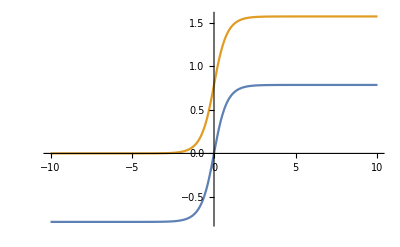

```mathematica
Plot[{f[x], ArcTan[ⅇ^(2 x)]},{x,-10,10}]
```

Izračunajmo še absolutno razliko začetnih vrednosti funkcije f (x) in njenega nedoločenega integrala. Začetna vrednost je vrednost funkcije v točki x = 0:

```mathematica
Abs[f[x]-ArcTan[ⅇ^(2 x)] /.x->0]
```

π/4

4. (3) Dan je trikotnik ABC z oglišči A(5, 3, -3), B(-3, -1, 5), C(3, 5, 5).

a) Izračunaj obseg trikotnika.

Definirajmo oglišča A, B, C, vektorje OverVector[AB], OverVector[AC], OverVector[CB], ter s pomočjo njihovih dolžin izračunajmo obseg trikotnika ABC, pri čemer poskusimo poenostaviti končni rezultat:

```mathematica
a={5,3,-3};
b={-3,-1,5};
c={3,5,5};
ab = b-a;
ac = c - a;
cb = c -b;
dAB = Norm[ab];
dAC= Norm[ac];
dCB = Norm[cb];
```

```mathematica
o=Simplify[dAB+dAC+dCB]
```

12 (1+√2)

b) Izračunaj ploščino trikotnika.

Ker imamo izračunane dolžine stranic trikotnika, lahko izračunamo njegovo ploščino kar po Heronovi formuli. Definirajmo še polobseg trikotnika in poskusimo poenostaviti končni rezultat:

```mathematica
s = o/2;
```

```mathematica
S=Simplify[Sqrt[s(s-dAB)(s-dAC)(s-dCB)]]
```

36

```mathematica
c) Izračunaj notranje kote trikotnika.
```

Notranje kote trikotnika lahko izračunamo kar s pomočjo prej izračunanih dolžin stranic in njegove ploščine z uporabo formul S=(a b sinγ)/2=(b c sinα)/2=(a c sinβ)/2:

```mathematica
α =ArcSin[2S/ (dAB * dAC)]
β =ArcSin[2S/ (dAB * dCB)]
γ =ArcSin[2S/ (dAC * dCB)]
```

π/4

π/4

π/2

d) Definiraj funkcijo, ki bo za dana oglišča trikotnika izračunalo njegovo težišče in izračunaj težišče trikotnika ABC.

Definiramo funkcijo T(A,B,C), ter vanjo kot parametre vstavimo oglišča A, B in C. Težišče trikotnika izračunamo po formuli T((X_A+X_B+X_C)/3, (Y_A+Y_B+Y_C)/3, (Z_A+Z_B+Z_C)/3):

```mathematica
T[a_, b_,c_]:=Module[{x1, x2, x3, y1, y2, y3, z1, z2, z3},
{x1, y1, z1}=a;
{x2, y2, z2}=b;
{x3, y3, z3}=c;
T={(x1+x2+x3)/3, (y1+y2+y3)/3, (z1 + z2 + z3)/3}
]
```

```mathematica
T[a, b, c]
```

{5/3,7/3,7/3}

e) Spodnja funkcija za dan vektor n⃗ in točko T vrne enačbo ravnine z normalnim vektorjem n⃗ in točko T. 
Določi enačbo množice vseh točk, ki so enako oddaljene od oglišč A in B.

```mathematica
EnacbaRavnine[n_, T_]:=Module[{a, b, c, d},
a = n[[1]];
b=n[[2]];
c=n[[3]];
d=Dot[n, T];
gcd = GCD[a,b,c,d];
a = a /gcd;
b= b / gcd;
c = c / gcd;
d= d/gcd;
a*x+b*y+c*z-d==0
]
```

Množica vseh točk, ki so enako oddaljene od oglišč A in B, je ravnina, ki poteka skozi razpolovišče daljice AB in ima OverVector[AB] za normalni vektor:

```mathematica
T1=a+1/2*ab
```

{1,1,1}

```mathematica
n1=ab
```

{-8,-4,8}

```mathematica
EnacbaRavnine[n1, T1]
```

1-2 x-y+2 z==0

f) Spodnja funkcija za dan vektor s⃗ in točko T vrne parametrično enačbo premice s smernim vektorjem s⃗ in točko T.
Določi enačbo množice vseh točk, ki so enako oddaljene od oglišč A, B in C.

```mathematica
EnacbaPremice[s_, T_]:=Module[{a, b, c, p, q, r},
a = s[[1]];
b=s[[2]];
c=s[[3]];
gcd = GCD[a,b,c];
a = a /gcd;
b= b / gcd;
c = c / gcd;
p = T[[1]];
q = T[[2]];
r = T[[3]];
{a,b,c}t+{p,q,r}
]
```

Množica vseh točk, ki so enako oddaljene od oglišč A in B, je premica, ki je presečišče ravnin, ki sta enako oddaljeni od točk A in B ter A in C. Njen smerni vektor določimo kot vektorski produkt obeh normalnih vektorjev, njeno poljubno točko pa kot rešitev sistema enačb ravnin, pri katerem ena od spremenljivk zavzame poljubno vrednost. Enako kot prej določimo enačbo ravnine, ki je enako oddaljena od točk A in C:

```mathematica
T2 = a+1/2*ac
```

{4,4,1}

```mathematica
n2=ac
```

{-2,2,8}

```mathematica
EnacbaRavnine[n2, T2]
```

-4-x+y+4 z==0

Izračunajmo smerni vektor premice, ki je enako oddaljena od oglišč A, B in C, kot vektorski produkt obeh normalnih vektorjev ravnin:

```mathematica
s=Cross[n1,n2]
```

{-48,48,-24}

Izračunajmo še točko premice, ki je enako oddaljena od oglišč A, B in C, kot rešitev sistema enačb ravnin, pri katerem ena od spremenljivk zavzame poljubno vrednost. Recimo naj bo y = 0:

```mathematica
y=0;
```

```mathematica
Solve[{EnacbaRavnine[n1, T1], EnacbaRavnine[n2, T2]},{x,z}]
```

{{x→2,z→3/2}}

```mathematica
T={2,0,3/2};
```

Od tod sledi, da premica p poteka skozi točko A(2, 0, 3/2). in ima smerni vektor s⃗=(-48, 48, -24) oziroma s⃗=(-2, 2, -1):

```mathematica
EnacbaPremice[s, T]
```

{2-2 t,2 t,3/2-t}

g) Določi središče očrtanega kroga trikotnika in njegov polmer.

Središče očrtanega kroga je presečišče med zgornjo premico in ravnino, ki jo določajo oglišča A, B in C. S pomočjo prej izračunanih vektorjev lahko določimo enačbo ravnine:

```mathematica
n3=Cross[ac, ab]
```

{48,-48,24}

```mathematica
EnacbaRavnine[n3, c]
```

-1+2 x-2 y+z==0

Če rešimo zgornjo enačbo tako, da koordinate x, y, z izrazimo z ustreznimi parametričnimi koordinatami točk prej dobljene premice, dobimo vrednost parametra t:

```mathematica
x=2-2t;
z=3/2-t;
y=2t;
Solve[EnacbaRavnine[n3, c], t]
```

{{t→1/2}}

Pri tej vrednosti parametra t premica seka ravnino v točki S, ki je središče očrtanega kroga:

```mathematica
t=1/2;
```

```mathematica
S=EnacbaPremice[s, T]
```

{1,1,1}

Polmer očrtane krožnice določimo kot razdaljo med S in poljubnim ogliščem trikotnika:

```mathematica
r=Norm[a-S]
```

6

h) Nariši trikotnik ABC in središče očrtane krožnice S v prostoru.

```mathematica
Graphics3D[{Point[S],Line[{a,b,c,a}]}]
```

-Graphics3D-

```mathematica
i) Zanemari aplikatne koordinate oglišč trikotnika in v nariši trikotnik in njemu očrtano krožnico v xy ravnini.
```

Izkaže se, da v Mathematici ni funkcije, ki bi v trirazsežnem prostoru izrisala krožnico, zato zanemarimo aplikatne koordinate (z koordinate) oglišč, pri čemer se spremeni le polmer očrtane krožnice:

```mathematica
a2={5,3};
b2={-3,-1};
c2={3,5};
S2={1,1};
```

```mathematica
r2=Norm[S2-a2]
```

2 √5

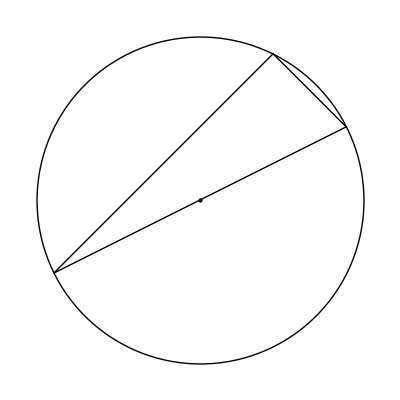

```mathematica
Graphics[{Point[S2],Line[{a2,b2,c2,a2}],Circle[S2,r2]}]
```

## Viri in literatura :

(1) How to draw a Circle in 3D on a sphere. Mathematica Stack Exchange. Junij 2018.
https://mathematica.stackexchange.com/questions/79524/how-to-draw-a-circle-in-3d-on-a-sphere (citirano 11.2.2019)
(2) Množice in izjavni račun. Matematika 1 (Spletna učilnica 2018/2019). Oktober 2018.
https://ucilnica.fmf.uni-lj.si/pluginfile.php/14286/mod_resource/content/1/Mnozice_izjave.pdf (citirano 12.02.2019)
(3) 1. kolokvij 2007. Linearna algebra (Spletna učilnica 2018/2019). Oktober 2018.
https://ucilnica.fmf.uni-lj.si/pluginfile.php/6055/mod_folder/content/0/1.kolokviji/PMK_1_ 2007.pdf (citirano 12.02.2019)